```mathematica
fermat=Import["/home/jirka/CPX/fermatM.csv"];
ss=Import["/home/jirka/CPX/ssM.csv"];
rm=Import["/home/jirka/CPX/rmM.csv"];

(* (i,rounds,p) rounds==-1->prime, rounds≥0->slozene p==2->prime p==0->composite*)
```

```mathematica
Length[Cases[fermat,{_,_,2}]](* pocet prvocisel*)
Length[Cases[fermat,{_,_,0}]](*pocet slozenych (lichych)*)
```

78496

851067

```mathematica
(*fermat si mysli prime, ve skutecnosti sloz. *)
Cases[fermat,{_,-1,0}] 
(*fermat si mysli slozene, ve skutecnosti prvocislo. *)
Cases[fermat,{_,_?(#≥0&),2}]
```

{}

{}

```mathematica
rounds={#,Length[Cases[fermat,{_,#,_}]]}&/@Range[50]
```

{{1,470},{2,38},{3,10},{4,5},{5,7},{6,1},{7,2},{8,1},{9,1},{10,0},{11,1},{12,2},{13,0},{14,0},{15,1},{16,0},{17,0},{18,1},{19,0},{20,1},{21,0},{22,0},{23,0},{24,0},{25,0},{26,1},{27,0},{28,0},{29,0},{30,1},{31,0},{32,0},{33,2},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,2},{45,0},{46,0},{47,0},{48,0},{49,1},{50,0}}

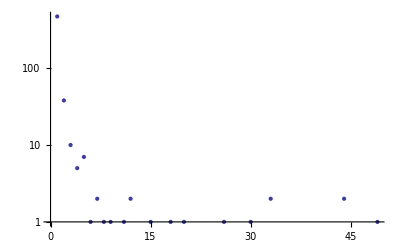

```mathematica
ListLogPlot[rounds]
```

```mathematica
Length[Cases[fermat,{_,0,_}]] (* odhaleny v prvnim kole *)
Length[Cases[ss,{_,0,_}]] 
Length[Cases[rm,{_,0,_}]]
```

850518

850835

850941

```mathematica
roundsSS={#,Length[Cases[ss,{_,#,_}]]}&/@Range[5]
roundsRM={#,Length[Cases[rm,{_,#,_}]]}&/@Range[5]
```

{{1,218},{2,13},{3,1},{4,0},{5,0}}

{{1,122},{2,4},{3,0},{4,0},{5,0}}